```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import["smalldem.tif",{"Geotiff","ElevationRange"}]
data=Import["smalldem.tif",{"Geotiff","Data"}];
```

{640.118,843.822}

```mathematica
colorf="DarkTerrain";
```

```mathematica
r1=ReliefPlot[data,ColorFunction->colorf,ImagePadding->None,Frame->False,ImageSize->{800,800}];
```

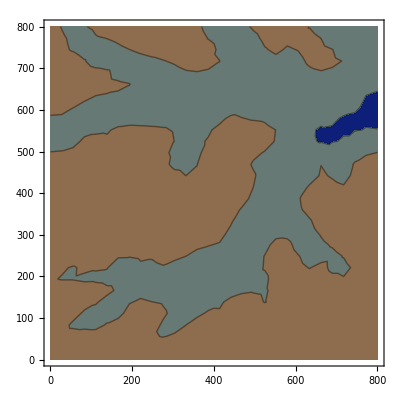

```mathematica
c1=ListContourPlot[data,MaxPlotPoints->30,Contours->Function[Range[650,850,100]],ColorFunction->colorf,PlotRange->{640,850}]
c2=ListContourPlot[data,MaxPlotPoints->30,Contours->Function[Range[650,850,50]],ColorFunction->colorf,PlotRange->{640,850}];
c3=ListContourPlot[data,MaxPlotPoints->30,Contours->Function[Range[650,850,20]],ColorFunction->colorf,PlotRange->{640,850}];
```

```mathematica
to3d[plot_,height_,opacity_]:=Module[{newplot},newplot =First@Graphics[plot];newplot=N@newplot /. {x_?AtomQ,y_?AtomQ}->{x,y,height} ;
newplot /. GraphicsComplex[xx__]->{Opacity[opacity],GraphicsComplex[xx]}];
```

```mathematica
ov=Show[{Graphics3D[to3d[c1,30,0.75]]},Graphics3D[to3d[c2,20,0.75]],Graphics3D[to3d[c3,10,0.75]],Lighting->"Neutral",BoxRatios->{1,1,0.8},Axes->True]
```

-Graphics3D-

```mathematica
pic=Reverse[ImageData[r1]];
```

```mathematica
bg=ListPlot3D[Table[1,{x,1,800,5},{y,1,800,5}],Mesh->None,VertexColors->{pic[[1;;800;;5,1;;800;;5]]},DataRange->{{1,800},{1,800}},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[bg,ov,PlotRange->All,Axes->None,BoxRatios->{1,1,1.5}]
```

-Graphics3D-